# Figure 7

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Time-dependent term ~σ_z

### Normal phase

```mathematica
g=1/2^(1/2); (*coupling*)
ξ=1/20;(*modulation amplitude*)
```

#### τ≠n/m T(E_0)

```mathematica
τ=5;
tintt=τ;
tf=50000;
Hsz[q_,p_,t_]=(q^2+p^2)/2-(1/2)*((1+ξ*Cos[(2π)*t/τ])^2+2*g^2*q^2)^(1/2);
```

```mathematica
(*Trajectory 1*)
pin=0.005;
qin=0.005;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1a=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.2;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2a=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=0.4;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3a=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=0.6;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4a=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=0.8;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5a=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=1.0;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6a=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

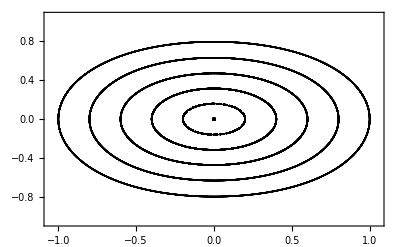

```mathematica
fig=ListPlot[{qprt1a,qprt2a,qprt3a,qprt4a,qprt5a,qprt6a},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.05,1.05},{-1.05,1.05}},LabelStyle->{16,Black}]
```

#### τ=T(E_0)

```mathematica
τ=8.8;
tintt=τ;
tf=10000;
Hsz[q_,p_,t_]=(q^2+p^2)/2-(1/2)*((1+ξ*Cos[(2π)*t/τ])^2+2*g^2*q^2)^(1/2);
```

```mathematica
(*Trajectory 1*)
pin=0.005;
qin=0.005;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.2;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.1;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=0.3;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=-0.2;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=-0.3;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 7*)
pin=0.0;
qin=0.4;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt7b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 8*)
pin=0.0;
qin=0.6;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt8b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 9*)
pin=0.0;
qin=0.8;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt9b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 10*)
pin=0.0;
qin=1.01;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt10b=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

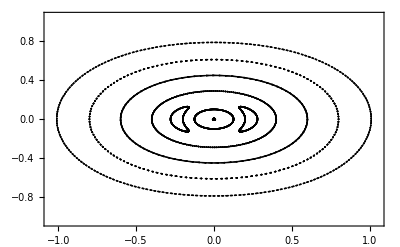

```mathematica
fig=ListPlot[{qprt1b,qprt2b,qprt3b,qprt5b,qprt7b,qprt8b,qprt9b,qprt10b},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.05,1.05},{-1.05,1.05}},LabelStyle->{16,Black}]
```

#### τ=1/2 T(E_0)

```mathematica
τ=4.4;
tintt=τ;
tf=50000;
Hsz[q_,p_,t_]=(q^2+p^2)/2-(1/2)*((1+ξ*Cos[(2π)*t/τ])^2+2*g^2*q^2)^(1/2);
```

```mathematica
(*Trajectory 1*)
pin=0.01;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.14;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.28;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.402;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=0.6;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=0.8;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 7*)
pin=0.0;
qin=1.0;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt7c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 8*)
pin=0.244;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt8c=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

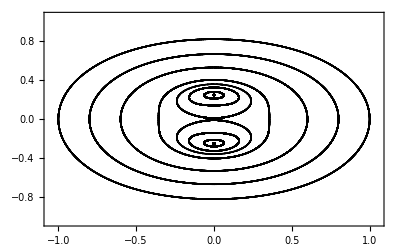

```mathematica
fig=ListPlot[{qprt1c,qprt2c,qprt3c,qprt4c,qprt5c,qprt6c,qprt7c,qprt8c},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.05,1.05},{-1.05,1.05}},LabelStyle->{16,Black}]
```

#### τ=1/4 T(E_0)

```mathematica
τ=2.2;
tintt=τ;
tf=50000;
Hsz[q_,p_,t_]=(q^2+p^2)/2-(1/2)*((1+ξ*Cos[(2π)*t/τ])^2+2*g^2*q^2)^(1/2);
```

```mathematica
(*Trajectory 1*)
pin=0.01;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.14;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=0.37;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=0.265;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=0.6;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=0.8;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 7*)
pin=0.0;
qin=1.0;
solt=NDSolve[{D[q[t],t]==D[Hsz[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsz[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt7d=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

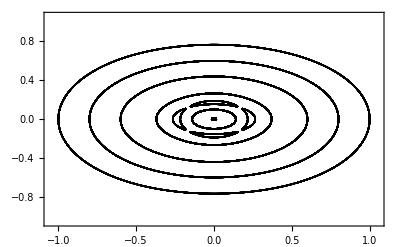

```mathematica
fig=ListPlot[{qprt1d,qprt2d,qprt3d,qprt4d,qprt5d,qprt6d,qprt7d},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.05,1.05},{-1.05,1.05}},LabelStyle->{16,Black}]
```

## Time-dependent term ~σ_x

### Normal phase

```mathematica
g=1/2^(1/2); (*coupling*)
ξ=1/20;(*modulation amplitude*)
```

#### τ≠n/m T(E_0)

```mathematica
τ=5;
tintt=τ;
tf=50000;
Hsx[q_,p_,t_]=(q^2+p^2)/2-(1/2)*(1+(ξ*Cos[(2π)*t/τ]+2^(1/2)*g*q)^2)^(1/2);
```

```mathematica
(*Trajectory 1*)
pin=0.005;
qin=0.005;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1i=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.2;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2i=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=0.4;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3i=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=0.6;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4i=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=0.8;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5i=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=1.0;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6i=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

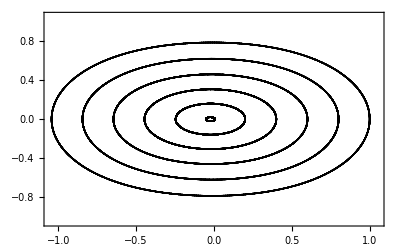

```mathematica
fig=ListPlot[{qprt1i,qprt2i,qprt3i,qprt4i,qprt5i,qprt6i},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.05,1.05},{-1.05,1.05}},LabelStyle->{16,Black}]
```

#### τ=T(E_0)

```mathematica
τ=8.8;
tintt=τ;
tf=50000;
Hsx[q_,p_,t_]=(q^2+p^2)/2-(1/2)*(1+(ξ*Cos[(2π)*t/τ]+2^(1/2)*g*q)^2)^(1/2);
```

```mathematica
(*Trajectory 1*)
pin=0.0;
qin=0.0;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1j=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.4;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2j=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=0.2;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3j=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=-0.2;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4j=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

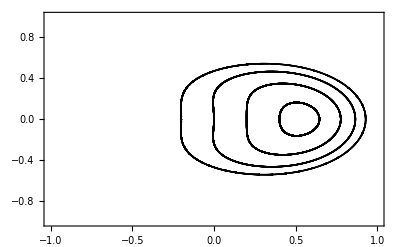

```mathematica
fig=ListPlot[{qprt1j,qprt2j,qprt3j,qprt4j},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1,1},{-1,1}},LabelStyle->{16,Black}]
```

#### τ=1/3 T(E_0)

```mathematica
τ=2.93;
tintt=τ;
tf=20000;
Hsx[q_,p_,t_]=(q^2+p^2)/2-(1/2)*(1+(ξ*Cos[(2π)*t/τ]+2^(1/2)*g*q)^2)^(1/2);
```

```mathematica
(*Trajectory 1*)
pin=0.0;
qin=0.13;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1k=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.01;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2k=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=0.5;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3k=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=0.7;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4k=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=0.9;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5k=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=-0.24;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6k=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 7*)
pin=0.0;
qin=-0.335;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt7k=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

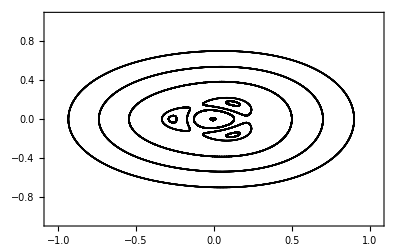

```mathematica
fig=ListPlot[{qprt1k,qprt2k,qprt3k,qprt4k,qprt5k,qprt6k,qprt7k},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.05,1.05},{-1.05,1.05}},LabelStyle->{16,Black}]
```

#### τ=1/5 T(E_0)

```mathematica
τ=1.76;
tintt=τ;
tf=20000;
Hsx[q_,p_,t_]=(q^2+p^2)/2-(1/2)*(1+(ξ*Cos[(2π)*t/τ]+2^(1/2)*g*q)^2)^(1/2);
```

```mathematica
(*Trajectory 1*)
pin=0.0;
qin=0.1;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt1l=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 2*)
pin=0.0;
qin=0.225;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt2l=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 3*)
pin=0.0;
qin=0.39;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt3l=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 4*)
pin=0.0;
qin=0.55;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt4l=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 5*)
pin=0.0;
qin=0.73;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt5l=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

```mathematica
(*Trajectory 6*)
pin=0.0;
qin=0.9;
solt=NDSolve[{D[q[t],t]==D[Hsx[q[t],p[t],t],p[t]],D[p[t],t]==-D[Hsx[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
qprt6l=Table[{q[t],p[t]}/.solt[[1]]/.t->i,{i,0,tf,tintt}];
```

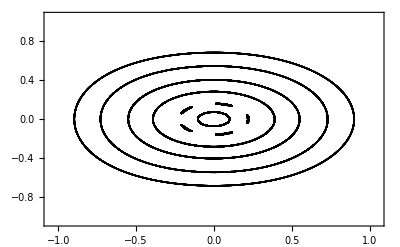

```mathematica
fig=ListPlot[{qprt1l,qprt2l,qprt3l,qprt4l,qprt5l,qprt6l},PlotStyle->{Black},Axes->False,Frame->True,PlotRange->{{-1.05,1.05},{-1.05,1.05}},LabelStyle->{16,Black}]
```